Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №5
 Функция Бесселя
Вариант №18

Выполнил: студент группы 0В01
Саматов Денис
Проверил: Богданов О.В.

Задание 1

-Graphics-

Пункт 1
	Используем табличные разложения, заложенные в данном математическом пакете

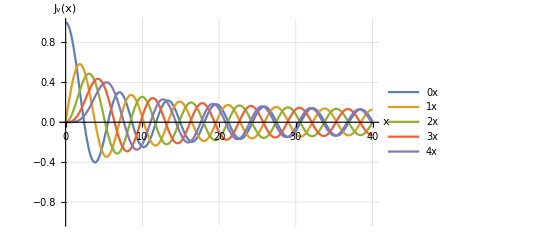

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x],BesselJ[4,x]},{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","J_v(x)"}]
```

Пункт 2
	Вычислим значения функции, как частичную сумму ряда

```mathematica
sumBessel[n_,v_]:=Sum[(-1)^k/(Gamma[k+v+1]*k!)*(x/2)^(2*k+v),{k,0,n}];
```

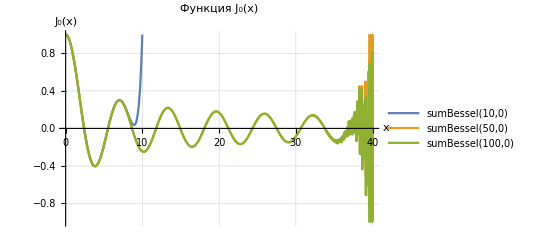

```mathematica
Plot[{sumBessel[10,0],sumBessel[50,0],sumBessel[100,0]},{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Функция J_0(x)",AxesLabel->{"x","J_0(x)"}]
```

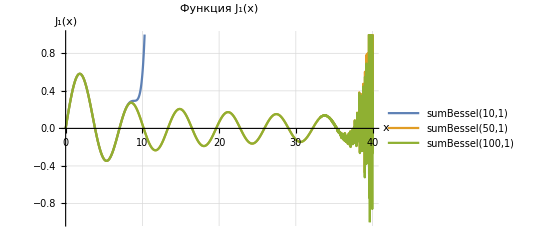

```mathematica
Plot[{sumBessel[10,1],sumBessel[50,1],sumBessel[100,1]},{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Функция J_1(x)",AxesLabel->{"x","J_1(x)"}]
```

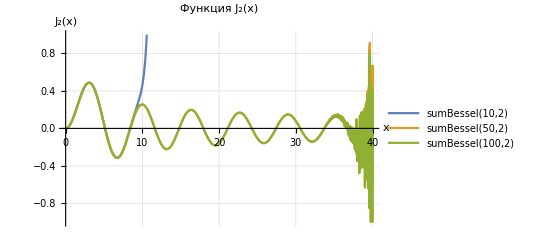

```mathematica
Plot[{sumBessel[10,2],sumBessel[50,2],sumBessel[100,2]},{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Функция J_2(x)",AxesLabel->{"x","J_2(x)"}]
```

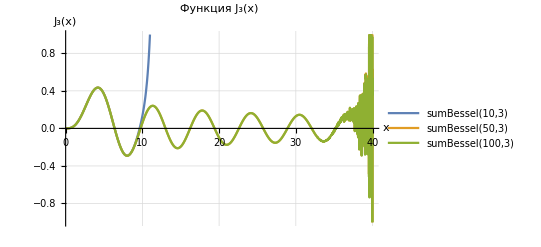

```mathematica
Plot[{sumBessel[10,3],sumBessel[50,3],sumBessel[100,3]},{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Функция J_3(x)",AxesLabel->{"x","J_3(x)"}]
```

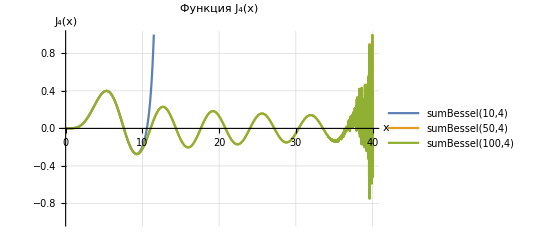

```mathematica
Plot[{sumBessel[10,4],sumBessel[50,4],sumBessel[100,4]},{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Функция J_4(x)",AxesLabel->{"x","J_4(x)"}]
```

Пункт 3
	Разобьем промежуток [0, 40] на промежутки [0, 25 + N/4] и [25 + N/4, 40], где N - это порядковый номер в списке группы.

На промежутке [0, 25 + N/4] вычислим значение функции как сумму ряда :

```mathematica
sumBessel[n_,v_]:=Sum[(-1)^k/(Gamma[k+v+1]*k!)*(x/2)^(2*k+v),{k,0,n}];
```

На промежутке [25 + N/4, 40] вычислим значение этих функций по асимптотической формуле:

```mathematica
sumRoundBessel[v_]:=√(2/(π*x))Cos[x-(π*v)/2-π/4];
```

```mathematica
plotList={};
For[i=0,i<=4,i++,
pieceplot=Piecewise[{{sumBessel[Infinity,i],0<=x<=25+18/4},{sumRoundBessel[i],25+18/4<=x<=40}}];
AppendTo[plotList,pieceplot];
]
```

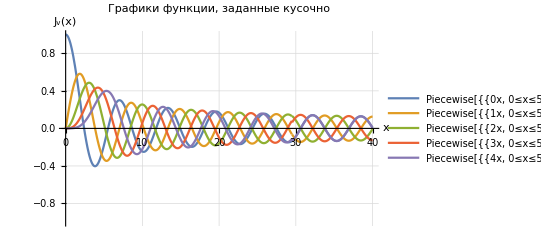

```mathematica
Plot[plotList,{x,0,40},PlotRange->{-1,1}, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Графики функции, заданные кусочно",AxesLabel->{"x","J_v(x)"}]
```

Задание 2
	Для случая из примера № 12 вашего варианта ИДЗ (вариант должен совпадать с вашим порядковым номером в списке  группы):
	А. Построить таблицу корней функций Бесселя и изобразить графически.
	Б. Проверить ортогональность системы функций Бесселя с соответствующим весом.
	В. Разложить функцию в ряд Фурье-Бесселя (или Дини) и построить на одном графике предложенную функцию и ее n-частичные суммы с n = 1, 2,…,5,…, 15… . Подобрать n-оптимальное , когда функция визуально совпадает с n-оптимальное -частичной суммой.

-Graphics-

```mathematica
f[x_]:=Piecewise[{{1,0<=x<=1},{-1,1<=x<=2}}];
```

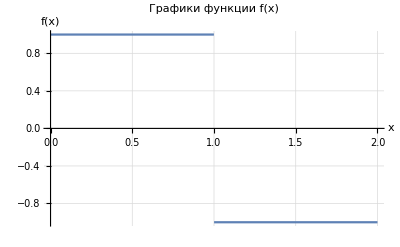

```mathematica
Plot[f[x],{x,0,2},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",PlotLabel->"Графики функции f(x)",AxesLabel->{"x","f(x)"}]
```

А . Построим таблицу корней функций Бесселя и изобразим графически.

Воспользуемся рекуррентным соотношением

```mathematica
D[BesselJ[0,γ],γ]
```

-BesselJ[1,γ]

```mathematica
zeros=N[Table[BesselJZero[1,k],{k,12}]];
num=Table[k,{k,12}];
Grid[Join[{{"Номер нуля функции J'_0(x)", "Значение нуля функции"}},Transpose[Join[{num},{zeros}]]],Frame->All]
```

Номер нуля функции J'_0(x) | Значение нуля функции
1 | 3.83171
2 | 7.01559
3 | 10.1735
4 | 13.3237
5 | 16.4706
6 | 19.6159
7 | 22.7601
8 | 25.9037
9 | 29.0468
10 | 32.1897
11 | 35.3323
12 | 38.4748

Изобразим графически корни функции Бесселя

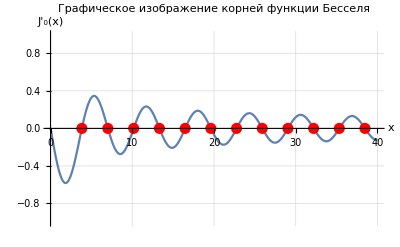

```mathematica
Plot[-BesselJ[1,γ],{γ,0,40},Epilog->{PointSize[0.02],Red,Point[Table[{BesselJZero[1,k],0},{k,12}]]},GridLines->Automatic,PlotRange->{-1,1},PlotLabel->"Графическое изображение корней функции Бесселя",AxesLabel->{"x","J'_0(x)"}]
```

Б. Проверим ортогональность системы, первых пяти функций Бесселя с соответствующим весом.

```mathematica
l=2;
```

```mathematica
orthogonalize={};
For[i=1,i<=5,i++,
For[j=1,j<=5,j++,
int=Integrate[x*BesselJ[0,x/l*zeros[[i]]]*BesselJ[0,x/l*zeros[[j]]],{x,0,2}];
AppendTo[orthogonalize,int]
]
]
```

Для этого построим матрицу

```mathematica
matrix=Partition[orthogonalize,5];
```

```mathematica
matrix//MatrixForm
```

(0.32443 | 4.96321×10^-15 | -4.03086×10^-15 | 3.5304×10^-15 | -3.09353×10^-15
4.96321×10^-15 | 0.180139 | 2.95681×10^-15 | -2.61448×10^-15 | 2.28711×10^-15
-4.03086×10^-15 | 2.95681×10^-15 | 0.124705 | 2.19292×10^-15 | -1.89237×10^-15
3.5304×10^-15 | -2.61448×10^-15 | 2.19292×10^-15 | 0.0953617 | 1.59913×10^-15
-3.09353×10^-15 | 2.28711×10^-15 | -1.89237×10^-15 | 1.59913×10^-15 | 0.0771973)

Заметим, что у матрицы все элементы будут нулевые, кроме главной диагонали. Таким образом, система функций Бесселя с соответствующим весом ортогональна.

В . Разложить функцию в ряд Фурье - Бесселя (или Дини) и построить на одном графике предложенную функцию и ее n - частичные суммы с n = 1, 2, …, 5, …, 15 … . Подобрать n - оптимальное , когда функция визуально совпадает с n - оптимальное - частичной суммой .

Так как в уравнении -Graphics- коэффициент β равен нулю, то разложение функции должно иметь следующий вид, -Graphics- Где b_0 находится  из следующего условия-Graphics- А коэффициенты b_i определяются по формуле -Graphics-
Данный случай описывается в книге:
	Кошляков Н. С. и др. Уравнения в частных производных математической физики. Учеб. пособие для мех.-мат. фак. ун-тов. М., «Высшая школа», 1970. - 712 с.

```mathematica
roots=N[Table[BesselJZero[1,k],{k,20}]];
```

```mathematica
b0=2/l^2*Integrate[x*f[x],{x,0,l}];
bm[γ_]:=((2*γ^2)/ ((γ^2)*BesselJ[0,γ]^2) )* 1/l^2*Integrate[x*f[x]*BesselJ[0,γ*x/l],{x,0,l}];
```

```mathematica
function1=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,roots[[;;1]]}];
function2=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,roots[[;;2]]}];
function5=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,roots[[;;5]]}];
function10=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,roots[[;;10]]}];
function15=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,roots[[;;15]]}];
```

Изобразим на графике предложенную функцию и ее разложение в ряд Фурье-Дини при n = 1, 2, 5, 10, 15.

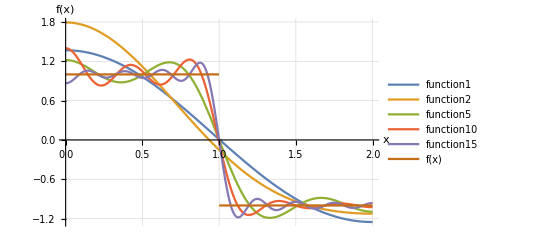

```mathematica
Plot[{function1,function2,function5,function10,function15,f[x]},{x,0,2},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"}]
```

Подберем n-оптимальное, при котором исходная функция будет визуально совпадать с разложением.

```mathematica
rootsn=N[Table[BesselJZero[1,k],{k,200}]];
```

Вычислим погрешность в точке x = 1, в зависимости от количества членов ряда разложения исходной функции

```mathematica
errorList={};
For[k=1,k<=150,k++,
error=N[bm[rootsn[[k+1]]]*BesselJ[0,rootsn[[k+1]]*1/l]]/2;
AppendTo[errorList,{k+1,Abs[error]}];

]
```

```mathematica
errorList
```

{{2,0.0809008},{3,0.0788236},{4,0.0472413},{5,0.0464183},{6,0.0333097},{7,0.0328767},{8,0.0257139},{9,0.0254481},{10,0.0209362},{11,0.0207567},{12,0.0176546},{13,0.0175254},{14,0.0152619},{15,0.0151644},{16,0.0134401},{17,0.013364},{18,0.0120067},{19,0.0119456},{20,0.0108495},{21,0.0107995},{22,0.00989576},{23,0.00985394},{24,0.00909609},{25,0.00906065},{26,0.00841598},{27,0.00838557},{28,0.00783049},{29,0.0078041},{30,0.00732115},{31,0.00729804},{32,0.00687402},{33,0.00685361},{34,0.00647835},{35,0.0064602},{36,0.00612576},{37,0.00610951},{38,0.00580956},{39,0.00579492},{40,0.00552439},{41,0.00551115},{42,0.00526592},{43,0.00525387},{44,0.00503054},{45,0.00501954},{46,0.00481531},{47,0.00480522},{48,0.00461774},{49,0.00460845},{50,0.00443574},{51,0.00442716},{52,0.00426754},{53,0.0042596},{54,0.00411163},{55,0.00410426},{56,0.00396671},{57,0.00395984},{58,0.00383166},{59,0.00382525},{60,0.0037055},{61,0.0036995},{62,0.00358739},{63,0.00358176},{64,0.00347657},{65,0.00347128},{66,0.00337239},{67,0.00336742},{68,0.00327428},{69,0.00326959},{70,0.00318171},{71,0.00317728},{72,0.00309423},{73,0.00309004},{74,0.00301143},{75,0.00300746},{76,0.00293295},{77,0.00292918},{78,0.00285846},{79,0.00285488},{80,0.00278766},{81,0.00278425},{82,0.00272027},{83,0.00271703},{84,0.00265607},{85,0.00265298},{86,0.00259483},{87,0.00259188},{88,0.00253635},{89,0.00253353},{90,0.00248045},{91,0.00247775},{92,0.00242696},{93,0.00242437},{94,0.00237573},{95,0.00237325},{96,0.00232661},{97,0.00232423},{98,0.00227949},{99,0.0022772},{100,0.00223423},{101,0.00223204},{102,0.00219074},{103,0.00218863},{104,0.00214891},{105,0.00214688},{106,0.00210865},{107,0.00210669},{108,0.00206986},{109,0.00206798},{110,0.00203248},{111,0.00203067},{112,0.00199643},{113,0.00199467},{114,0.00196163},{115,0.00195994},{116,0.00192802},{117,0.00192639},{118,0.00189555},{119,0.00189397},{120,0.00186415},{121,0.00186262},{122,0.00183377},{123,0.0018323},{124,0.00180437},{125,0.00180294},{126,0.0017759},{127,0.00177451},{128,0.00174831},{129,0.00174697},{130,0.00172157},{131,0.00172026},{132,0.00169563},{133,0.00169436},{134,0.00167046},{135,0.00166923},{136,0.00164603},{137,0.00164483},{138,0.0016223},{139,0.00162114},{140,0.00159925},{141,0.00159812},{142,0.00157684},{143,0.00157574},{144,0.00155505},{145,0.00155399},{146,0.00153386},{147,0.00153282},{148,0.00151323},{149,0.00151222},{150,0.00149315},{151,0.00149217}}

Из полученных результатов видно, начиная с n = 111 значение функции очень медленно меняется. Если построить графики функций при n = 111 и n = 151 визуально различия почти не наблюдаются.

```mathematica
function111=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,rootsn[[;;111]]}];
```

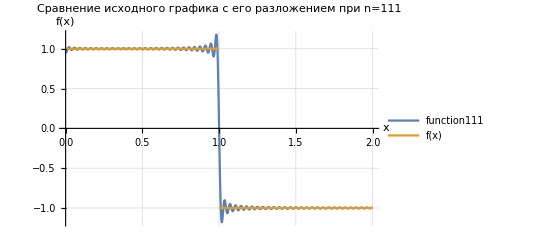

```mathematica
Plot[{function111,f[x]},{x,0,2},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"Сравнение исходного графика с его разложением при n=111"]
```

```mathematica
function151=b0+Sum[bm[m]*BesselJ[0,m*x/l],{m,rootsn[[;;151]]}];
```

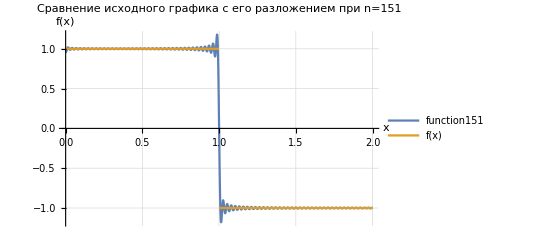

```mathematica
Plot[{function151,f[x]},{x,0,2},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"Сравнение исходного графика с его разложением при n=151"]
```

Таким образом, n -  оптимальное равно 111.

Вывод
	В ходе выполнения лабораторной работы были построены графики функции Бесселя -Graphics-различными способами.
	1) Используя табличные разложения, заложенные в данном математическом пакете.
	2) Вычисляя значения функции, как частичную сумму ряда.
	Стоит отметить, что при использовании встроенных методов графики были построены без ошибок. При построении графиков с помощью частичных сумм, были получены ошибки, что можно наблюдать на графиках. Это связано скорее всего с большими значениями в знаменателе, так как там находится факториал.
	Также в этой лабораторной работе проверена ортогональность системы функций  Бесселя с соответствующим весом. А также была разложена кусочная функция в ряд Фурье-Дини и подобрано n-оптимальное, при котором кусочная функции визуально совпадает с n-оптимальное - частичной суммой. Для представления исходной функции в ряд  Фурье-Дини была изучена дополнительная литература.
	Кроме этого, были изучены новые функции:  BesselJ[], BesselJZero[].